```mathematica
$HistoryLength = 0
<<NonStandartImportExport`
```

0

```mathematica
file = FileNameJoin[{$NonStandartImportExportDirectory, "Resources", "MarmousiModel.segy"}]
```

E:\Test Items\Wolfram Language\Mathematica\Projects\NonStandartImportExport\Resources\MarmousiModel.segy

```mathematica
AbsoluteTiming[data = NonStandartImport[file, "SGY"];]
```

{0.055122,Null}

```mathematica
data["BinaryHeader"]
```

{JobID→0,LineNumber→0,ReelNumber→0,NumberDataTraces→298,NumberAuxTraces→0,IntervalReelRecord→5000,IntervalFieldRecord→0,NumberOfSamplesForReel→300,NumberOfSamplesForField→0,SamplesFormatCode→1,CDPFold→0,TraceSortingCode→0,VerticalSumCode→0,SweepFrequencyAtStart→0,SweepFrequencyAtEnd→0,SweepLength→0,SweepTypeCode→0,TraceNumberOfSweepChannel→0,SweepTraceTaperLengthAtStart→0,SweepTraceTaperLength→0,TaperType→0,CorrelatedDataTraces→0,BinaryGainRecovered→0,AmplitudeRecoveryMethod→0,MeasurementSystem→2,ImpulseSignal→0,VibratoryPolarityCode→0}

```mathematica
data["BinaryHeader", 1]
```

JobID→0

```mathematica
data["BinaryHeader", 1 ;; 4 ;; 2]
```

{JobID→0,ReelNumber→0}

```mathematica
data["BinaryHeader", {4, 6}]
```

{NumberDataTraces→298,IntervalReelRecord→5000}

```mathematica
data["BinaryHeader", "JobID"]
```

0

```mathematica
data["Headers", 2]
```

{0,0,0,2,0,0,0,2,0,0,0,1,0,0,0,72,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data["Headers", 2, 16]
```

72

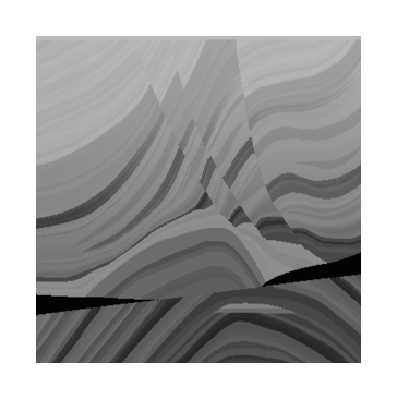

```mathematica
ArrayPlot[Transpose[data["Tracks"]]]
```

```mathematica
AbsoluteTiming[unloaded = NonStandartImport[file, "SGY", "Loading" -> "Delayed"];]
```

{0.0229922,Null}

```mathematica
unloaded["Headers"]
```

SEGYUnloaded[{ConvertFunction→Function[{NonStandartImportExport`Extensions`SEGY`Private`bytes},NonStandartImportExport`Extensions`SEGY`Private`bytes],DataFile→E:\Test Items\Wolfram Language\Mathematica\Projects\NonStandartImportExport\Resources\MarmousiModel.segy,DataSize→240,Positions→{3600,5040,6480,7920,9360,10800,12240,13680,15120,16560,18000,19440,20880,22320,23760,25200,26640,28080,29520,30960,32400,33840,35280,36720,38160,39600,41040,42480,43920,45360,46800,48240,49680,51120,52560,54000,55440,56880,58320,59760,61200,62640,64080,65520,66960,68400,69840,71280,72720,74160,75600,77040,78480,79920,81360,82800,84240,85680,87120,88560,90000,91440,92880,94320,95760,97200,98640,100080,101520,102960,104400,105840,107280,108720,110160,111600,113040,114480,115920,117360,118800,120240,121680,123120,124560,126000,127440,128880,130320,131760,133200,134640,136080,137520,138960,140400,141840,143280,144720,146160,147600,149040,150480,151920,153360,154800,156240,157680,159120,160560,162000,163440,164880,166320,167760,169200,170640,172080,173520,174960,176400,177840,179280,180720,182160,183600,185040,186480,187920,189360,190800,192240,193680,195120,196560,198000,199440,200880,202320,203760,205200,206640,208080,209520,210960,212400,213840,215280,216720,218160,219600,221040,222480,223920,225360,226800,228240,229680,231120,232560,234000,235440,236880,238320,239760,241200,242640,244080,245520,246960,248400,249840,251280,252720,254160,255600,257040,258480,259920,261360,262800,264240,265680,267120,268560,270000,271440,272880,274320,275760,277200,278640,280080,281520,282960,284400,285840,287280,288720,290160,291600,293040,294480,295920,297360,298800,300240,301680,303120,304560,306000,307440,308880,310320,311760,313200,314640,316080,317520,318960,320400,321840,323280,324720,326160,327600,329040,330480,331920,333360,334800,336240,337680,339120,340560,342000,343440,344880,346320,347760,349200,350640,352080,353520,354960,356400,357840,359280,360720,362160,363600,365040,366480,367920,369360,370800,372240,373680,375120,376560,378000,379440,380880,382320,383760,385200,386640,388080,389520,390960,392400,393840,395280,396720,398160,399600,401040,402480,403920,405360,406800,408240,409680,411120,412560,414000,415440,416880,418320,419760,421200,422640,424080,425520,426960,428400,429840,431280}}]

```mathematica
unloaded["Headers"][2]
```

SEGYUnloaded[{ConvertFunction→Function[{NonStandartImportExport`Extensions`SEGY`Private`bytes},NonStandartImportExport`Extensions`SEGY`Private`bytes],DataFile→E:\Test Items\Wolfram Language\Mathematica\Projects\NonStandartImportExport\Resources\MarmousiModel.segy,DataSize→240,Positions→5040}]

```mathematica
NonStandartLoad[unloaded["Tracks"][1]]
```

{1500.,1500.,1500.,1509.65,1632.77,1662.5,1665.,1667.5,1686.32,1766.12,1775.,1777.5,1780.,1784.12,1707.04,1669.09,1690.,1692.5,1695.,1697.5,1700.,1701.98,1729.74,1758.03,1760.,1762.5,1765.,1761.23,1653.41,1632.5,1635.,1637.5,1646.6,1679.98,1685.,1687.5,1690.,1692.5,1695.,1731.16,1750.,1752.5,1755.,1749.18,1651.13,1657.84,1715.,1717.5,1720.,1742.2,1796.2,1807.68,1810.,1812.5,1815.,1817.5,1809.47,1758.91,1709.55,1679.87,1732.96,1798.91,1764.43,1726.68,1730.,1719.48,1695.,1697.44,1704.34,1727.7,1800.86,1879.04,1880.,1883.02,1859.79,1836.98,1840.,1842.5,1845.,1894.56,1920.,1922.5,1925.,1921.71,1821.83,1802.81,1789.93,1783.92,1871.28,1892.5,1895.,1893.08,1841.53,1832.5,1835.,1789.79,1770.,1772.5,1775.,1777.5,1780.,1781.94,1812.04,1853.1,1860.,1862.5,1865.,1867.5,1889.56,1984.84,1995.,1991.04,1910.23,1857.95,1825.,1831.2,1879.88,1887.3,2145.63,2452.41,2450.,2453.75,2457.5,2461.25,2469.97,2496.86,2502.5,2506.25,2510.,2513.75,2517.5,2521.25,2525.,2516.19,2487.96,2486.14,2490.,2493.75,2497.5,2505.91,2595.8,2619.7,2577.01,2532.81,2506.64,2503.75,2507.5,2517.02,2597.21,2637.1,2642.5,2646.25,2650.,2653.75,2657.5,2661.25,2665.,2668.75,2672.5,2676.25,2680.,2664.23,2627.5,2631.25,2635.,2638.75,2642.5,3529.53,4069.99,4130.76,4242.49,4258.74,4244.66,4121.56,4166.21,4237.46,3984.45,2883.79,2812.5,2812.44,2741.49,2731.25,2737.5,2975.49,3053.73,2852.63,2842.5,2846.87,2829.99,2831.25,2837.5,2845.61,2874.97,2886.25,2892.5,2898.75,2905.,2911.25,2917.5,2924.99,2946.65,2956.25,2962.5,2968.75,2975.,2941.96,2867.5,2890.07,3078.98,3015.49,3012.5,2971.18,2955.,2960.53,3002.19,3044.48,3082.57,3243.47,3262.5,3268.75,3386.64,3951.83,4000.,4000.,4000.,3432.06,2500.,2500.,2500.,2547.37,2650.,2505.7,2440.,2459.2,2500.,2500.,2857.14,5274.59,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5500.,5342.47,3600.,3300.,3300.,3297.,3231.62,3201.36,3200.,3200.,3200.,3200.,3200.,3200.,3200.,3201.24,3140.64,3059.32,3050.,3050.,3050.,3049.05,3118.53,3516.18,3550.,3550.,3550.,3550.,3550.,3535.01,3342.47,3254.06,3250.,3250.,3250.,3403.2,3827.49,3892.65,3733.76,3700.,3700.,3700.,3700.,3674.79,3610.9,3599.77}